Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario B: mid water influx, water_in=500

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
win=500;
ws=0;
ws=alpha*(win-beta);
wt= win-ws;
```

Define system without fire effects:

```mathematica
hdot[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
wdot[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Nullclines and fixed points:

```mathematica
hnull=Simplify[Solve[hdot[H,W]==0,H]]
hnulleq=hnull[[All,1,2]];
hnull1=hnulleq[[1]];
hnull2=hnulleq[[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→386.667-0.6 W}}

```mathematica
wnull=Simplify[Solve[wdot[H,W]==0,H]]
wnulleq=wnull[[All,1,2]];
wnull1=wnulleq[[1]];
(*wnull2=wnulleq[[2]];*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→(8000.+295. W-0.6 W^2)/(-100.+W)}}

```mathematica
fp=Simplify[Solve[hdot[H,W]==0 && wdot[H,W]==0,{W,H}]]
fpnum=Transpose[{fp[[All,1]][[All,2]],fp[[All,2]][[All,2]]}];
fp1=fpnum[[1]]
fp2=fpnum[[2]]
fp3=fpnum[[3]]
(*fp4=fpnum[[4]]*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→-25.7681,H→0.},{W→307.692,H→202.051},{W→517.435,H→0.}}

{-25.7681,0.}

{307.692,202.051}

{517.435,0.}

Plot things

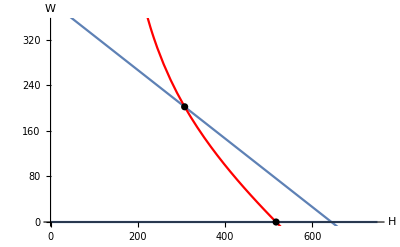

```mathematica
ph1=Plot[hnull1,{W,0,750},AxesLabel->{W,H}];
ph2=Plot[hnull2,{W,0,750}];
pw1=Plot[wnull1,{W,0,750},PlotStyle->Red];
(*pw2=Plot[wnull2,{W,0,750},PlotStyle->Red];*)
points=ListPlot[{fp2,fp3},PlotStyle->Black];
Show[ph1,ph2,pw1,points,PlotRange->{0,350}]
```

Stability Analysis

Stable node fixed point

```mathematica
j11=D[hdot[H,W],H]/.fp[[2]];
j12=D[hdot[H,W],W]/.fp[[2]];
j21=D[wdot[H,W],H]/.fp[[2]];
j22=D[wdot[H,W],W]/.fp[[2]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```

{-0.531102,-0.0953811}

Unstable node fixed point (saddle?)

```mathematica
j11=D[hdot[H,W],H]/.fp[[3]];
j12=D[hdot[H,W],W]/.fp[[3]];
j21=D[wdot[H,W],H]/.fp[[3]];
j22=D[wdot[H,W],W]/.fp[[3]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```

{-0.333884,0.175652}